```mathematica
path = "C:\\Users\\enego\\OneDrive\\Documents\\GitHub\\durhack22\\ML\\mathematics_dataset-v1.0\\train-easy"
allFiles=FileNames["*.txt", path];
allData=AssociationMap[Import[#]<>Import[StringReplace[#,"train-easy"->"train-hard"]] <>Import[StringReplace[#,"train-easy"->"train-medium"]] <>Import[StringReplace[#,"train-easy"->"interpolate"]]&, allFiles];
```

C:\Users\enego\OneDrive\Documents\GitHub\durhack22\ML\mathematics_dataset-v1.0\train-easy

```mathematica
allData[[-1]]
```

```mathematica
allData = KeyMap[StringDelete[StringSplit[#,"\\"][[-1]],".txt"]&, allData];
```

```mathematica
Keys[allData][[1]]
```

algebra__linear_1d_composed

```mathematica
largeQuestion = StringSplit[#, "\n"][[1;;;;2]]&/@ allData;
```

```mathematica
questions = RandomSample[#,500]&/@ largeQuestion
```

```mathematica
naturalQuestions = StringRiffle[StringSplit[#]]&/@ StringReplace[#,{"-"-> " minus ", "+"-> "plus", "="-> "equals", "**"-> "", "."-> "", "*"-> " multiply ", "("-> "open bracket ", ")"-> " close bracket " }]&/@ questions
```

```mathematica
getAsso[key_] := Normal[AssociationThread[naturalQuestions[key],key&/@naturalQuestions[key]]]
```

```mathematica
plainData = Association[Flatten[getAsso[#]&/@Keys[naturalQuestions]]]
```

```mathematica
bert = NetModel["DistilBERT Trained on BookCorpus and English Wikipedia Data"]
```

NetChain[<>]

```mathematica
embedData = KeyMap[bert[#,TargetDevice->"GPU"]&,Association[Normal[plainData]]];
```

$Aborted

```mathematica
mixedData = RandomSample[Normal[embedData], Length[Normal[embedData]]];
Length[mixedData]
```

23973

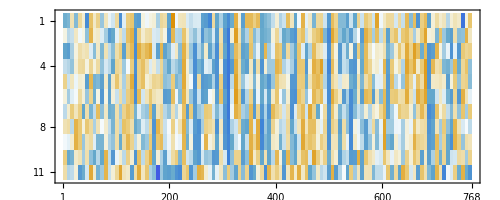

```mathematica
MatrixPlot[Keys[mixedData][[1]]]
```

```mathematica
{traingingData, vtData} = TakeDrop[mixedData,Floor[0.75*Length[mixedData]]];
```

```mathematica
{testData, validationData} = TakeDrop[vtData, Floor[0.8 * Length[vtData]]];
```

```mathematica
Length[testData]
```

4795

```mathematica
network = NetChain[{DropoutLayer["Input"->{"Varying",768}],NetBidirectionalOperator[LongShortTermMemoryLayer[150]](*, GatedRecurrentLayer[50]*),(*NetMapOperator[LinearLayer[30]],*)LongShortTermMemoryLayer[56],AggregationLayer[Total,1], LinearLayer[56],SoftmaxLayer[ "Output" -> NetDecoder[{"Class",Keys[questions]}]] }]
```

NetChain[<>]

```mathematica
trainedNet = NetTrain[network,traingingData, ValidationSet->validationData, TargetDevice->"GPU"]
```

NetChain[<>]

```mathematica
NetMeasurements[trainedNet, testData, "ErrorRate"]
```

0.116371

```mathematica
Union[Values[Association[traingingData]]]
```

{algebra__linear_1d,algebra__linear_1d_composed,algebra__linear_2d,algebra__linear_2d_composed,algebra__polynomial_roots,algebra__polynomial_roots_composed,algebra__sequence_next_term,algebra__sequence_nth_term,arithmetic__add_or_sub,arithmetic__add_or_sub_in_base,arithmetic__add_sub_multiple,arithmetic__div,arithmetic__mixed,arithmetic__mul,arithmetic__mul_div_multiple,arithmetic__nearest_integer_root,arithmetic__simplify_surd,calculus__differentiate,calculus__differentiate_composed,comparison__closest,comparison__closest_composed,comparison__kth_biggest,comparison__kth_biggest_composed,comparison__pair,comparison__pair_composed,comparison__sort,comparison__sort_composed,measurement__conversion,measurement__time,numbers__base_conversion,numbers__div_remainder,numbers__div_remainder_composed,numbers__gcd,numbers__gcd_composed,numbers__is_factor,numbers__is_factor_composed,numbers__is_prime,numbers__is_prime_composed,numbers__lcm,numbers__lcm_composed,numbers__list_prime_factors,numbers__list_prime_factors_composed,numbers__place_value,numbers__place_value_composed,numbers__round_number,numbers__round_number_composed,polynomials__add,polynomials__coefficient_named,polynomials__collect,polynomials__compose,polynomials__evaluate,polynomials__evaluate_composed,polynomials__expand,polynomials__simplify_power,probability__swr_p_level_set,probability__swr_p_sequence}

```mathematica
questions["algebra__linear_2d"]
```

{Solve 2*l + 16 = 2*m, -4*m + 22 = -5*l - 15 for l.,-3,Solve 87*l - 83*l + 14*n = 372, 4*n - 96 = 4*l for l.,Solve 2*y - 2*k - 2 - 10 = 0, -4*k = 20 for y.,Solve -3*v - 3*s + 6 = 0, -11 = -v - 2*s - 12 for v.,Solve 2*g + 40 = 5*p + 5, -3*g = 5*p - 10 for g.,Solve -p - 4*v = 8 + 7, 5*v + 50 = 5*p for p.,Solve 2*d + 5*u - 44 = 0, 360*d - u + 4 = 362*d for d.,Solve -220*t + 4*p = -219*t - 3, 5*t + 2*p = -29 for t.,Solve -26*f = 2*q - 27*f - 7, 4*f + 12 = 0 for q.,Solve 0 = 3*d - 5*x - 3, 4*x + x = -2*d + 2 for d.,Solve 2*g = r - 1, 2*g = -4*r - 0*g - 26 for r.,Solve u + 6 = 3*j, 13*j - 2*u - 10 = 8*j for j.,4,-15,Solve -6 = -3*b + 3*l, -3*l - 2 - 7 = -4*b for b.,Solve -4*p - 2429 = -11*x - 2422, 0 = -x - p + 17 for x.,Solve 4*v + 4*j = -4, v + 2*j - 1 = -6 for v.,Solve -m = -3*a - 9, 76*a = -4*m + 78*a + 16 for m.,Solve -3*a + 4*d + 1 = 0, 4*a + 2*d + 0*d + 28 = 0 for a.,Solve -3*c + 5*h - 7 = 0, 2*c - 10 = -3*h + 17 for c.,Solve 10 = -h - 3*b, -h - 19*b + 20 = -22*b for h.,-5,Solve 5*a - 2*i + 5 = -i, 5*i = -3*a + 25 for a.,Solve 2*f + 5358*r = 5356*r - 2, 0 = f - 4*r + 6 for f.,5,2,Solve -u + 1 = l, 5*u - 5 - 4 = -4*l for u.,Solve r - 48*l = -51*l + 17, 2*r + 2 = 3*l for r.,Solve 4*m + 5*c - 29 = 0, -225 = -5*m + 2*c - 230 for m.,Solve i = -2*n + 6*i + 15, -n - 4*i = 25 for n.,Solve -5*p = 4*b + 5, 3*b - 3*p - 3 = -0 for b.,Solve -24 = -5*j - 2*u, -51*u = -56*u - 15 for j.,-16,Solve 0 = 3*x - j + 5, -3*j = -4*x - 5 - 5 for x.,Solve -f = -m + 4, -45*m - 20 = 3*f - 50*m for f.,Solve 2*o + 4*j + 26 = 0, 3*j + 17 - 2 = 0 for o.,Solve 142*m - 140*m - o = 11, 5*m - 26 = 2*o for m.,Solve 3*m + 2*o + 3 = 0, 4*o + 4 = -4*m - 0*o for m.,7,Solve 4*k + 28 = 4*h, -2*k - h - 8 = -0*k for k.,Solve 0 = 5*z - 3*i + 27, 24*i - 19*i = -7*z - 1 for z.,38,Solve a = 36*x - 38*x + 4, -4*a = -4*x + 8 for a.,7,16,Solve 4*f + 7 = 3*t, 0 = 2*f + 3*t - 8 - 11 for f.,Solve -5*l - 10 = -0*c + c - 9, 3*c = 12 for l.,Solve 3*h = 3*k - 9, -3*h + 34 - 37 = 0 for k.,1,3,1,-47,Solve -2*c = -8, 10*g + 4*c = 6*g - 24 for g.,Solve -9*g + 95 = -4*g + 21*u, 0 = 4*u - 20 for g.,Solve 3 = g, 4*g + 0*g - 5*g = 4*q + 13 for q.,Solve 16*p - 14*p = 2*f + 18, 4*p + 18 = -2*f for p.,Solve 20 = -5*t + 5*j, 305*j = -6*t + 310*j - 22 for t.,Solve -63*j = -67*j - p - 23, 5*j + 2*p + 28 = 0 for j.,Solve -175*w + 177*w = -5*g - 10, -4*g - 8 = 0 for w.,Solve 12 = h - 4*h + 3*c, -3*h = 5*c + 20 for h.,Solve -60 + 15 = r - 10*n + 5, 50 = -4*r + 10*n for r.,Solve 18*b - 14*b = -5*g - 40, b - 2*g - 3 = 0 for b.,4,Solve -5*u - 11 + 23 = 3*x, -20*x - 17 = u for x.,Solve 81*t - 77*t + 16 = -3*r, -2*r - 3*t - 9 = 0 for r.,Solve 424 = 2*j + 434, 2*a + 3*j = -25 for a.,Solve 5*a + 3*f + 10 = -2*f, 0 = -a + 2*f - 2 for a.,Solve 4*l - 15 = v, 2223*l + 4*v = 2226*l - 8 for l.,Solve 4*s = -14 - 6, 2*s = y - 14 for y.,Solve 4*a - 6 = 2*k, 7131*k - 7136*k + 13 = -3*a for k.,Solve w + 2*b = -673 + 671, 3*b = -15 for w.,Solve -23 = -5*j + 4*w - 15, 3*w + 25 = -j for j.,Solve 3*y - f + 4 = 0, 3*y - 37 = 7*y + 5*f for y.,Solve -3*x - 5*k = -5 + 3, -4*k = -x - 5 for x.,5,0,Solve 3*t = 5*l - 41 + 28, 20 = 4*l for t.,Solve 5*y - 4*u + 15 = 0, 112*y - 15 = 56*y + 61*y - u for y.,Solve -c = -5*h - 5 + 25, -5*c = -3*h + 34 for c.,26,Solve 0 = -169*r + 171*r - 4*i - 4, -2*i - 10 = r + 2*i for r.,Solve 5*u = -x + 23, 5*x + u - 1 = 18 for x.,Solve 3*r - 9 = -2*p, 0 = -4*p - 9383*r + 9387*r - 22 - 10 for p.,1,Solve 0 = u - 3*x + x - 4, 8 = 2*u + 4*x for u.,Solve -4*n = -4*l + 12, 69*n - 70*n = 4*l - 7 for l.,Solve -1055*x + 1067*x = 5*t - 123, -3 = -x - 4*t for x.,Solve -2*s = v - 15, 5*v + 259 = -32*s + 466 for s.,Solve -16 = 4*a + 4*h, -h - 5 = 34*a - 32*a for a.,Solve 3*h - 115 = -5*k - 128, 10*h + 3*k = -16 for h.,5,Solve -3*i + 4*x - 38 = 0, 19*x - 23*x = -i - 26 for i.,54,5,Solve -2*w + w + 5*f + 4 = 0, 2*f + 7 = -5*w for w.,-2,Solve -2*z - 6 = 4*u, 4*u + 5*z + 0 + 3 = 0 for u.,Solve -7*b = 3*s + 41, 53*s - 19 = 3*b + 54*s for b.,Solve -2*o + 52*h - 47*h + 4 = 0, -2*o + 4 = -3*h for o.,10,-4,Solve 4*j + h + 8 = 0, -2*j - 4*h - 4 = -h for j.,Solve -3 = -c - 4*a, 0*c - 24 = 4*c - 2*a for c.,Solve 3*m = 5*l - 4, -22*m + 17*m + 2*l = 13 for m.,Solve 3*j - 19 + 16 = -2*f, -3*f = -j - 10 for f.,Solve 3*p - 5*t - 32 = -p, -3*t + 3 = 5*p for p.,Solve v - 7*g = -5*g + 7, 2*v = -2*g - 4 for v.,Solve 2 - 9 = -4*i - 5*u, -i - 4*u - 1 = 0 for i.,Solve -5*j + 1 = f, f + 6*j = 5*j - 3 for f.,-4,Solve -28*a + 25 = 2*z - 33*a, 3*z - 5*a - 43 = -13 for z.,Solve 0 = f + 6, -42*g + 46*g - 2*f = 20 for g.,Solve -7*r + 5*x = -100, 18*r + 4*x = 17*r - 47 for r.,-3,Solve 5*g + 3*b = -18, -6*b + 11 = -5*g - 2*b for g.,Solve 2*k + 21 = 7*k - 4*w, -3*k + w + 14 = 0 for k.,-46,Solve 3*g = 5*o - 25, -g - 6*o + 7*o - 5 = 0 for g.,Solve 0 = 4*g + 3*c + 29, -4*g - 16 + 2 = -2*c for g.,-25,Solve -11 = -3*b + 4, -5*c + 2*b = 35 for c.,-13,Solve 4*h + 2*r - 4 = 0, -22*h - 3*r = -17*h - 6 for h.,Solve 0 = -25*g + 3*c + 122, 3*g - 3*c - 2 = 2*g for g.,Solve -12 = -5*b + 2*b + 3*c, 4*b - 14 = 2*c for b.,9,-3,Solve -5*s = 5*c - 30, -c - 3 = -2*s - 0 for s.,14,-5,Solve s + 4*s - 4*g - 18 = 0, -2*g = 3*s - 2 for s.,Solve -4*l - 583*b = -581*b + 6, 4*b = 3*l + 21 for l.,-68,Solve -258*u + 260*u + 5*o = 11, -5 = -3*u + 4*o for u.,Solve 0 = 3*p + 3*u + 12, p = -3*u + 8*u + 2 for p.,Solve 5*i = 4*j - 17, 2*j - 5*i + 3 = 24 for j.,Solve 2*f + 2*k + 401 = 409, 0 = 2*f - 5*k - 1 for f.,5,1,22,Solve 2*o = -44*h + 40*h + 16, 0 = -h + 5*o - 40 for h.,-7,-4,Solve -4*u - 79*f + 9 = -80*f, 2*u - 3 = f for u.,-5,11,Solve -2*g = h - 40, 3*h + 101 = -4*g + 179 for h.,3,4,Solve 35 = 4*a + 3*p, -p = -2*a - 4 + 9 for a.,Solve 2*a + 16 = 4*i, -120*i = -121*i - 3*a + 4 for i.,Solve -11*z - 23*z + 3*z - 62 = 0, p = 4*z + 10 for p.,-5,-40,Solve 0 = -4*b - 5*y + 3, -10*b + 5*b = 3*y - 7 for b.,Solve 5*w = -5*v - 45, -323*w - 3*v = -327*w - 22 for w.,-1,Solve -2*n = -4*u + 2, u - 2*n - 13 = n for u.,Solve 3*x = -10 - 2, 5*t = 2*x + 3 for t.,Solve -f - 3*d - 6 = 0, -9*f = -6*f + 2*d + 4 for f.,Solve v + 3*n = -18, 0 = -22*v + 19*v - 4*n - 29 for v.,-27,Solve -4*z + 17 = -5*w, -2*w + 3*z - 29 = 30 - 55 for w.,7,5,-3,Solve -2*t + 7 = -o + 2*o, 6*t = o + 1 for o.,Solve -20 = 4*y - 4*s, -s + 16 = -5*y + 3 for y.,7,Solve 4*x - 4*m + 149 = 145, x = 3*m - 13 for x.,Solve 0 = -0*j + 3*j + 5*c - 12, 19 = -4*j + 5*c for j.,4,Solve -825*x + 821*x + u - 26 = 0, 0 = x - 2*u + 3 for x.,Solve -u + 2*y = 3, 0 = -4*u + 3*y - 6*y - 1 for u.,Solve -6*j - 352 = -5*j - 116*c, -217*j = -218*j - c - 1 for j.,Solve -2*l + 1 = 4*w + 15, -12 = 4*w for l.,Solve -4*l - 8 = 3*o - 0, 3*l - 11 = 2*o for l.,Solve 0*c + j = -5*c - 23, 12 = -4*j for c.,Solve -4*t = -6*t - 3*k - 2, -k + 1 = t for t.,Solve 19 = -2*z + 3*i, -4 + 25 = -3*z + 2*i for z.,Solve 0 = -3*t - 4722*f + 4719*f - 3, 4*t + 2*f = 0 for t.,Solve 0 = -4*m - f - 217 + 227, 0 = 4*m + 2*f - 4 for m.,Solve 56*s = -3*u + 52*s - 32, -u - 3*s - 19 = 0 for u.,Solve 5*q + 6 + 14 = 0, -4*q = z + 13 for z.,Solve -a + 29 = -5*y, 4*y + 18 = -a + 2 for y.,Solve -158*q + 157*q = 8*s + 24, 2*s = -4*q - 6 for s.,-1,Solve 0 = 154*b - 149*b - o + 2, -6 = -2*b - 3*o for b.,-12,Solve 3*h = 4*b - 11, -5*h - 15 = -2*h for b.,Solve 0 = -3*l - 7 + 4, 5 = -3*f - 2*l for f.,Solve 0 = g + 5*l + 10, g + 0*l - 2*l = 4 for g.,Solve -68*w - 4*i = -63*w + 2 + 28, 0 = -i - 5 for w.,Solve 4*l + 13 = 128*h - 123*h, 3*l = -h + 14 for h.,Solve -3*h = 33471*z - 33474*z + 18, 5*z - 36 = 2*h for h.,Solve -4*k = -3*m + 7*m, 2*k = 4*m - 30 for k.,Solve 7*a + 4*n - 453 + 419 = 0, 4*a + 4*n = 16 for a.,0,Solve 0 = 5*d + 809*s - 810*s - 2, 0 = -4*d - 3*s - 6 for d.,Solve -5*p - 3*u + 5 = 0, -9 = 4*p + u - 6 for p.,Solve 3*c + 2*q + 8 = 0, 2*q = 3*c - q + 3 for c.,Solve -4*y + 29 = -2*o + 3, -5*o = 4*y - 5 for y.,4,Solve 0 = -z - 2*o, 0 = -8*z + 3*z + 5*o - 30 for z.,Solve m = 3*w + 4, -9*w - 14 = 4*m - 6*w for m.,Solve 0 = -2*v - 5*h - 4, -120*v + 121*v + 2 = -5*h for v.,-1,20,Solve 2161*u - 2160*u = 5*a - 7, 5*a - 16 = -2*u for u.,Solve 2*s = s - 5*j + 26, 4*j = -s + 21 for s.,Solve 5*p + 11 = 2*f, -4*p = -2*f - 1 + 11 for f.,Solve 5*m - 2*a + 17 = 0, -128 = 2*m + 4*a - 126 for m.,Solve -5*w + 26 = -y, -4*w - y - 609 + 610 = 0 for w.,-4,Solve 0 = s - r, -116*s + 112*s - 20 = r for s.,-5,Solve 8*r - 3*g = 2018 - 1940, 3*r = 4*g + 35 for r.,Solve 3*k + 13 = -2*l, -3*l - 12 = -2*k + 5*k for l.,Solve 4*p = -4*v, v = 5*p + 4 + 20 for p.,Solve -4*l = -o + 2*o + 15, l + 5*o = 1 for l.,Solve 73*q + 4*o = 75*q - 8, 5*o + 32 = -3*q for q.,Solve 2*o - 2*h - 2 = -0*o, -2*o - 7 = -5*h for o.,6,1,-24,Solve 1060*x - 1062*x = -5*d + 13, -5*x - 46 = d for d.,Solve -12*x - 41*c = -39*c - 16, 0 = -5*x + 4*c + 26 for x.,Solve 0 = 3*s - 3*m - 1771 + 1792, 5*s + 2*m = 0 for s.,Solve 0 = -4*v - 20, -4 = 3*g - 4*g + v for g.,2,5,Solve 4*h - 5*d = -80, -3*h + 525*d - 522*d = 57 for h.,-5,Solve 5*j = -5*b + 10, b + 3 = 4*j + 5 for j.,Solve -5*d - 5*y = -10, -2*d + 14*y - 17*y + 11 = 0 for d.,18,-3,Solve 4*l - 3 = l, -3*a - 4*l + 4 = 0 for a.,Solve 2*g + 5*z - 12 = 0, 13 = 3*g - 0*z + 5*z for g.,-10,Solve -6 = 3*k + 5*z, -2*k - 24 = -5*k + 5*z for k.,0,Solve 2*q - 9 = -3*p, 0*p + 5*p - 5*q - 15 = 0 for p.,Solve 2*t + 4*d = -2 + 18, 5*t + 16 = 4*d for t.,Solve 0 = -4*d + l, 4*d + 5*l + 0*l = 0 for d.,Solve 5*s = -22*z + 24*z - 8, 3*s + 6*z = 24 for s.,7,Solve 0 = -4*b + 4*r - 32, 0 = 23*b - 20*b - r + 18 for b.,-3,Solve a + 4*r = -8, 3*a + 2*r = 13 - 7 for a.,-11,Solve -2*y + j + 1 - 7 = 0, 2*y + 22 = 5*j for y.,Solve -2*s - 2*z = -40444 + 40432, 3*s + 4*z - 23 = 0 for s.,-5,Solve -3*u - 2*t = 8, 7*u = 4*u + 5*t - 1 for u.,Solve -27 = g + 5*q, 99*q - 31 = 3*g + 104*q for g.,Solve -22 = 6*t - t + 2*u, -t + 1 = -5*u for t.,Solve -4*v + 5*a - 6 = -27, 20 = 4*v - 4*a for v.,Solve -3*r - 2*x = 16, -37 = 6*r - 16*x + 21*x for r.,Solve 2*n = -2*j - 9 + 7, -7 = -n + j for n.,Solve 4*g + 78*x - 83*x + 9 = 0, -5*g - 10 = -5*x for g.,Solve 48 = -5*w - 3*i + 66, -5*w + 3*i = -12 for w.,Solve -4*x = 10*p + 54, 2 = -48*x + 51*x - p for x.,36,4,Solve -4*x + 4*j + 12 = x, 8 = 3*x - 2*j for x.,13,Solve -2*w - 3*g - 11 = 0, -6*g + 14 = -4*w - 4*g for w.,Solve 0 = -5*a - 2*n, 3*a - 266*n + 268*n = 4 for a.,Solve 21 = 2*x + 3*f, -x + 2*x + 6 = 4*f for x.,Solve 5*l - 26 = -2*r, -1410*r + 1409*r + 7 = l for r.,Solve 23*o + 2*n = 22*o + 4, 0 = -4*o - n - 5 for o.,Solve w - 8 + 3 = 0, -2*u = 3*w - 17 for u.,Solve -4*m - 2*d - 24 = 0, 0*d = d + 2 for m.,1,-1,Solve -6*i + 8*w = 13*w - 50, 2*i - 5*w = -10 for i.,Solve -13 = -s - 3*m, 3*m - 15 = -3*s + 2*m for s.,Solve 645*b - 643*b + 3*p = -4, -5*p = -b - 2 for b.,3,Solve -2*b = -4*v + 8, 3*b - 16 + 8 = v for v.,3,-4,-1,Solve 3*b + 4*j + 8 = 3*j, 2*b + 2*j = -4 for b.,5,Solve -2 = -a + 524*z - 525*z, -10 = -2*z for a.,Solve 0*a + 8 = -2*i - 2*a, 5 = -5*a for i.,Solve 7*j = 3*j + 3*z, -7*z + 8*z + 4 = 0 for j.,Solve 4*u = -4*x + 4, -2*u - u = -5*x + 5 for x.,42,Solve -i = -4*f - 25, 38 = 2*i - 42*f + 37*f for i.,Solve 2587*i = 2584*i - 5*w + 64, 6*w - 66 = 0 for i.,Solve -2*p + 1 - 10 = z, -3*p + 5*z = 7 for p.,16,Solve -5*f + 18 = m, -23*m + 19*m = 2*f for f.,Solve 6 = 2*v + 173*g - 169*g, 0 = 5*v - 3*g + 37 for v.,Solve k - 3*a = -15, 40 = -4*k + 3*a + 16 for k.,Solve 6*b - 3*b - 1 = 2*p + 7, 2*p + 2 = 0 for b.,Solve y = -4*s - 16, 3*y + 2*s + 222 = 204 for y.,Solve -3*x = 15, -152 = -p - 4*x - 166 for p.,Solve 0 = -6*s + 2*s + w - 7, -2*w = 2*s + 16 for s.,Solve 182*w - 181*w - 311 = 15*u, -46 = 2*u + w for u.,Solve -6*t = 18, 3515*k + t - 13 = 3511*k for k.,Solve 19*d - 3 = 18*d, 5 = 51*p - 46*p - 5*d for p.,3,Solve 0*g + 12 = -4*g, -2*l - 5*g - 23 = 0 for l.,Solve -2*i = 5*d - 44, i + 5*d - 713 = -681 for i.,Solve 3*w + 31*q - 19 = 36*q, -3*w - 3*q = -3 for w.,Solve z - t = 10, 2*z + 144*t - 145*t = 15 for z.,Solve 5*z = 5*u - 20, -21 = 132*u - 136*u + 5*z for u.,5,-1,Solve 3*r + 7 = 2*i + 4*r, 0 = -3*i + 4*r - 6 for i.,Solve -l + 2*l - 5*c = -23, -4*c = 4*l - 4 for l.,-1,Solve -2*f = k + 8, 0 = -5*k - 3*f - 1 - 18 for k.,Solve -5*m + 2634*s + 25 = 2633*s, 4*m + 3*s - 1 = 0 for m.,Solve 3*i = 2*o + 20, 26*i - 25*i = -4*o - 26 for o.,0,Solve -2*b - 8 = -4*c, 0 = 14*c - 18*c + 4 for b.,Solve -20 = 2*q - 6*q + l, 4*q = -3*l + 20 for q.,Solve -31*l - 4*d = -29*l + 24, 0 = -l + 2*d + 4 for l.,-33,1,Solve -23 = -5*m - 3*a, -2*a = -91*m + 98*m - 30 for m.,-5,Solve -5*j - 2*o = 3, -16 = -3*j + o - 20 for j.,Solve -234*w = -5*c - 229*w - 10, -5*w + 25 = 0 for c.,37,Solve 0*z = -2*z + j, -j = 3*z + 5 for z.,4,3,Solve -4*l = -4*x + 4, 7 = -13*x + 10*x + l for x.,-49,Solve 3*v = 6*v - 3*u - 3, -4*v = -2*u - 2 for v.,Solve -5*q + 112 - 133 = h, 0 = -5*h - 7*q - 33 for h.,Solve -3*f = 43*t - 39*t - 15, -f = -t - 5 for t.,3,-11,Solve 0 = 4*c - 3*q + 14, 13 = -45*c + 42*c + q for c.,-8,2,Solve -m + 31*s - 4 = 28*s, 0 = -4*m + s + 17 for m.,20,Solve -2*n + 40 = 35*i - 39*i, 5*n = 5*i + 75 for i.,Solve 3*u - m + 8 = 0, 38*u + 8 = 40*u - 4*m for u.,Solve -3*j = -l - 17, 19*j - 3*l - 23 = 17*j for j.,-7,Solve 5*u - 5*o = -38 + 58, 0 = -4*u + 5*o + 24 for u.,Solve -4*o - 7*f + 2*f = 0, -5*o - 5*f = 0 for o.,Solve -3*c - 11 = -2*t, -3*t - 196 = 3*c - 205 for t.,Solve 3*y + 0 = -2*d - 3, 5*d - 3*y = -39 for d.,Solve 3*w - l = -3, 54 = -3*w + 2*l + 48 for w.,Solve 1 = -2*a + c - 8, 5*a + 5*c = 0 for a.,Solve 13 = 4*c - x, -5*x - 5 - 16 = 2*c for c.,Solve 4*d - 7 = 4*i + 9, i + 5*d = 26 for i.,Solve -3*p + 15 = 0, b + p = -3*p + 24 for b.,-3,-12,Solve 4*r + 5*y = -33, 5*r + 126*y - 123*y = -25 for r.,-10,-5,-4,Solve -b - 1 = 2*y, 0 = 2*b + y - 5*y + 2 for b.,Solve -4*n + 2*l = -2, 3*n - 4857*l - 5 = -4859*l for n.,-27,-1,Solve -926*s + 931*s + 5 = -q, 3*s - 3*q + 21 = 0 for s.,Solve -2*c = 4*r + 63 - 95, -c + 18 = 3*r for r.,Solve -2*y - 4*t = -8, -3*y - t + 4 = -8 for y.,Solve -2*x + 19 = 3*u, -18*x + 14*x = 3*u - 23 for u.,Solve -2*f - 3*q - 5 = 0, 48 = -2*f - q + 49 for f.,-24,Solve f + 50 = -3*v + 36, -4*v - 10 = -3*f for v.,3,Solve -4*i + 5*n - 7 = 30, i + 18 = 3*n for i.,Solve 5*u - 4 = -q, -4 = 6*u - 9*u - q for u.,Solve -5*k + 6 = 2*a - 6*a + 23, -4*k - 13 = -3*a for a.,1,Solve -104562 = -2*t + 6*c - 104596, 5*t + 35 = 5*c for t.,Solve 2*b + 3*s = -5, -4*s + 34 = 4*b + 46 for b.,Solve -4*q - 16 = 0, -3*q + 2 - 17 = 3*m for m.,Solve 110*y - 113*y = -3*g - 6, g = -5*y + 16 for y.,Solve 2*z + 4*c = 14, -351*c - 10 = -z - 356*c for z.,Solve 5*s = 4*d + 18 + 22, 23 = -3*d + 2*s for d.,Solve -c + 15 = 5*j, -35*j + 28 = -4*c - 33*j for c.,0,Solve 0 = 2*b + 4*r + 10, -3*r - 26 = b - 16 for b.,Solve -13*n = -2*k - 4, 3085*k = 3083*k + 2*n - 26 for k.,2,Solve f = -n - 6, -6 = 5*f - 26 + 75 for n.,2,Solve 66*p - 65*p + 16 = 5*l, -3*p - l + 16 = 0 for p.,85,Solve 3*b - 3*o = 54, 10*b - 9*b + 8*o = -9 for b.,0,Solve -3*u = 3*l + 27, -173*u + 5*l - 5 = -168*u for u.,Solve n = -3*i + 5*i - 5, -4*n + 2*i - 8 = 0 for n.,Solve -2*v = -0*v + 2*z - 4, -5*v + 16 = 2*z for v.,5,Solve -2 = i - 5, -2*n - 11*i + 12 = -37 for n.,Solve 2*p - 5*h = -15, -p - 44429*h + 44425*h = -25 for p.,Solve -8 = -w - 12, 5*k = 5*w + 35 for k.,Solve 32 = z + 5*j + 41, -2*z + j + 15 = 0 for z.,Solve 9 = 3*i - 3*v, 15 = -4*i - v + 27 for i.,3,Solve h - 2*s = -5 + 9, 0 = 4*h + 4*s + 32 for h.,Solve 9*g = 5*f - 85, g - 3*f + 8*f - 85 = 0 for g.,4,Solve -q + 23 - 12 = 0, 4*i = 2*q - 38 for i.,Solve -2*g - 5*h - 3 - 10 = 0, h + 6 = 3*g for g.,Solve -12 = 4*w, 2*w = 5*k + w - 28 for k.,Solve 5*i + 7*h - 35 = 0, -4*i + 5*h = -497 + 522 for i.,1,Solve -61*s - 3*d + 15 = -57*s - 14, -3*d + 21 = 0 for s.,Solve 0 = r + 468 - 462, 0 = b + 3*r - 13 + 32 for b.,Solve -4*c + 5*g + 32 = -c, 4 = -2*c - 3*g for c.,2,-12,Solve 0 = -3*r - 4*k + 14, -4512*k = -4*r - 4497*k + 39 for r.,Solve 5*z = 0, j + 3*z - 16 = -3*j for j.,Solve t - 5*y = 3 - 6, t + 3*y - 5 = 0 for t.,-5,18,5,Solve -4*k + 20 = 7*w - 3*w, 0 = w + 3*k - 13 for w.,Solve -5*y = 5*c + 45, -2*y - c + 2 = 15 for y.,Solve 5*d + 20 = l + 47, -l + d - 7 = 0 for l.,-26,Solve -5*i - 5*h = -9*h + 17, -4*i - 4*h = 28 for i.,Solve -22 = -5*o - 4 + 2, 0*o - 19 = -5*w - o for w.,Solve 6*a + 45 = x, -18*a + 33 = -21*a - 3*x for a.,Solve d = 2*t + 32 - 31, -11 = -3*t + 4*d for t.,Solve 7*x + 31 = b, -x = 2*b + 3639 - 3641 for x.,Solve w + 18 = -5*n, -3*n + w = -4*n - 2 for n.,8,Solve 5*l + 2*g + 9 = 0, 0*l + 5*l - 546*g + 541*g = -30 for l.,Solve 2097*c - 2096*c + 16 = 4*a, 0 = -4*a - 3*c + 16 for a.,-5,Solve 141*s = -5*o + 135*s - 88, 46 = 3*o - 4*s for o.,3,3,Solve -6*z = n + 2, -143*z - 2 = -138*z + n for z.,59,Solve -36*a + 31*a - 2*w = -15, -5*w + 6 = 2*a for a.,Solve -5*i + 22 = 3*x, 16*x - 7*x - i - 34 = 0 for x.,0,Solve -5*u + 67 - 112 = -4*n, -n - 15 = 4*u for u.,Solve 4*h + 2 + 4 = -2*k, -3*k = -h - 12 for k.,4,Solve -t - 30*g + 8 = -28*g, 24 = -2*t + 4*g for t.,-1,-3,Solve 5*b = -25, 6 = -i + 2423*b - 2424*b for i.,-3,Solve -g + 2*t = -5, -2*t + 4*t + 4 = 0 for g.,Solve 4*x - 14 = i, 54*x + 3*i + 6 = 57*x for x.,0,-16,Solve -5*f = -0*s + 3*s - 20, 0 = -5*f - 4*s + 25 for f.,-4,-5,Solve 5*v + 3*x = 13, -39*v = 22*x - 20*x - 80 for v.,Solve 4*f - 5 - 2 = n, 4*n - 3*f + 2 = 0 for n.,Solve -j + 0*j + 3*o = 11, 5*o - 13 = -j for j.,30,Solve 8*n = 10*n + 2*z + 2, -2 = -4*n - z for n.,5,-4,-30,Solve -3*b = q - 13 + 2, 8 = 3*b + 4*q for b.,Solve 2*u - 3*q - 239 = -236, 4*q + 4 = -4*u for u.,-4,Solve -9*h - 3 = 15, -5*y - h = -18 for y.,Solve 5*o - x + 14 = 0, 9*o = 11*o + x for o.,Solve 2*g + 17 = 3*b, 372*b + 3*g = 369*b + 12 for b.,Solve 3 = 3*k - t - 2, 3 = -k + 5*t for k.,Solve -5*a = 4*r - 7, r - 5*a + 62 = 70 for r.,Solve 4*r - 2*i = 49 - 43, -3*r - 12 = 4*i for r.,Solve 0 = -2*w + 6, -q - 4360*w - 20 = -4365*w for q.,4,5,Solve -15*r = -12*r + 2*p - 24, 52 = 4*r - 4*p for r.,Solve 7 = -3*r - 3*s + 5*s, -3*r + 7 = 2*s + 18 for r.,Solve 0 = i + 3*s - 18 + 1, 2*i + 6 = 4*s for i.,Solve 5*j - 9*j + 8 = 0, -4*j + 13 = k for k.,Solve k - 7 = l, -45*l - 8 = -2*k - 41*l for k.,Solve 2*i = 4*o + 6, 0 = -2*o - 363*i + 362*i - 1 for o.,Solve -15*j = -15, -j - 69 + 28 = -3*n for n.,-17,-1,Solve -5*n - 4313 = 3*x - 4316, 0 = -n - 4*x + 4 for n.,Solve -4*u = 7*p - 6*p + 31, -5*p = -11*u - 62 for p.,Solve -2*v - 2*h = -3*h - 8, 2*v - 3*h = 12 for v.,Solve -2*b - 10*p + 7*p + 3 = 0, 5*p = -2*b + 1 for b.,-6,2,Solve -q = -34*y - 65, -q + 3*y = -0 - 3 for q.}

```mathematica
trainedNet[bert["Solve 3x **  minus 11x minus 13 equals 0", TargetDevice->"GPU"], TargetDevice->"GPU"]
```

arithmetic__mixed

```mathematica
TextRecognize[-Graphics-]
```

```mathematica
Expression[questions[[1]][[1]]]
```

Expression[Suppose -1382*k + 1464*k = 11972. Solve -32*w + 78 = -k for w.]

```mathematica
TextRecognize[]//AbsoluteTiming
```

{0.0004229,Suppose -1382«k + 1464«k = 11972. Solve -32«w + 78 = -k for w.}

```mathematica
ToString[ToExpression["n ^ 5"]]
```

5
n

```mathematica
ToString["4n ^ 5", StandardForm, CharacterEncoding->"ASCII"]
```

\!\(\*RowBox[{"\"4n ^ 5\""}]\)

```mathematica
NetDrop[trainedNet,1]
```

NetChain[<>]

```mathematica
Export["C:\\Users\\enego\\OneDrive\\Documents\\GitHub\\durhack22\\ML\\bert.onnx", bert]
```

C:\Users\enego\OneDrive\Documents\GitHub\durhack22\ML\bert.onnx